## Type I Variant model

## 1. Possible Scenarios

```mathematica
Quit[]
```

#### FeynArts

```mathematica
(* Activate FeynArts *)
$LoadFeynArts=True;
$FeynCalcSartupMessages=False;
<<FeynCalc`
$FAVerbose=0;
FAPatch[PatchModelsOnly->True];
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

Successfully patched FeynArts.

```mathematica
(* Load FR model *)

modelfile="Type_I_variant";

InitializeModel[modelfile, GenericModel->modelfile]
```

True

```mathematica
(* Decay width *)
topo=CreateTopologies[0,1->2];
decaydiag[ii_]:=InsertFields[topo,{S[2]}->{F[ii],F[ii]},InsertionLevel->{Particles},Model->modelfile,GenericModel->modelfile]
```

```mathematica
RawdecAmp[ii_]:=
CreateFeynAmp[decaydiag[ii]]/.{FeynAmpDenominator->FAFeynAmpDenominator,FeynAmpList->FAFeynAmpList,NonCommutative->FANonCommutative,PolarizationVector->FAPolarizationVector,DiracSpinor->Spinor}
FCdecamp[ii_]:=(FCFAConvert[RawdecAmp[ii],List->False,DropSumOver->True,ChangeDimension->4,UndoChiralSplittings->True,IncomingMomenta->{p1},OutgoingMomenta->{p2,p3}])//Contract//DiracSimplify

AmpSq[ii_]:=Simplify[DiracSimplify[FermionSpinSum[FCdecamp[ii]ComplexConjugate[FCdecamp[ii]]]]]
```

```mathematica
(4π)/(32 π^2 mphi)1/2 1/2 AmpSq[1]/.Pair[Momentum[p2],Momentum[p3]]->1/2 mphi^2+mnl1^2
```

(lphiN^2 mnl1^2 mphi)/(16 π mN1^2)

```mathematica
(4π)/(32 π^2 mphi)1/2 1/2 AmpSq[7]/.Pair[Momentum[p2],Momentum[p3]]->1/2 mphi^2+mchi^2
```

(lphichi^2 mphi)/(16 π)

```mathematica
(4π)/(32 π^2 mphi)1/2 1/2 AmpSq[7]/.Pair[Momentum[p2],Momentum[p3]]->1/2 mphi^2+mchi^2/.lphichi->3*^-3/.mphi->0.05
```

8.95247×10^-9

```mathematica
(* Decay width of Subscript[n, heavy] *)
topo=CreateTopologies[0,1->2];
decaydiag[ii_]:=InsertFields[topo,{F[6]}->{S[1],F[1]},InsertionLevel->{Particles},Model->modelfile,GenericModel->modelfile]
```

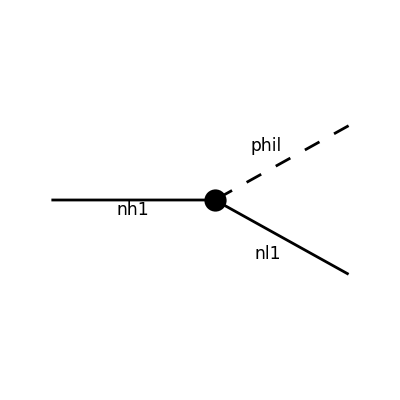

FeynArtsGraphics()(([]))

```mathematica
topo=CreateTopologies[0,1->2];
decay=InsertFields[topo,{F[4]}->{S[2],F[1]},InsertionLevel->{Particles},Model->modelfile,GenericModel->modelfile];
Paint[decay,ColumnsXRows->{1,1},Numbering->None,SheetHeader->False,ImageSize->{150,150}]
```

```mathematica
RawdecAmp[ii_]:=
CreateFeynAmp[ii]/.{FeynAmpDenominator->FAFeynAmpDenominator,FeynAmpList->FAFeynAmpList,NonCommutative->FANonCommutative,PolarizationVector->FAPolarizationVector,DiracSpinor->Spinor}
FCdecamp[ii_]:=(FCFAConvert[RawdecAmp[ii],List->False,DropSumOver->True,ChangeDimension->4,UndoChiralSplittings->True,IncomingMomenta->{p1},OutgoingMomenta->{p2,p3}])//Contract//DiracSimplify

AmpSq[ii_]:=Simplify[DiracSimplify[FermionSpinSum[FCdecamp[ii]ComplexConjugate[FCdecamp[ii]]]]]
```

```mathematica
(4π)/(32 π^2 mN1)1/2 AmpSq[decay]/.Pair[Momentum[p1],Momentum[p3]]->mN1^2/2//Simplify
```

(lphiN^2 mnl1 (mN1+2 mnl1))/(8 π mN1)

```mathematica
(4π)/(32 π^2 mN1)1/2 AmpSq[decay]/.Pair[Momentum[p1],Momentum[p3]]->mN1^2/2/.mN1->10/.mnl1->3 10^-8/.lphiN->0.1
```

1.19366×10^-11

### Cross section Calculations

#### Amplitudes n_l n_l → n_l n_l

```mathematica
topo=CreateTopologies[0,2->2];
diagSI[ii_,jj_]:=InsertFields[topo,{F[ii],F[ii]}->{F[jj],F[jj]},InsertionLevel->{Particles},Model->modelfile,GenericModel->modelfile]
```

```mathematica
(* Diag SI among same mass eigenstates *)
diagSI11 = diagSI[1,1];
diagSI22 = diagSI[2,2];
diagSI33 = diagSI[3,3];

diagSI11 = DiagramDelete[diagSI11, {1,4,7}];
diagSI22 = DiagramDelete[diagSI22, {1,4,7}];
diagSI33 = DiagramDelete[diagSI33, {1,4,7}];

(* Diag SI among different mass eigenstates *)
diagSI12=diagSI[1,2];
diagSI13=diagSI[1,3];
diagSI23=diagSI[2,3];

diagSI12 = DiagramDelete[diagSI12, {1,4,6}];
diagSI13 = DiagramDelete[diagSI13, {1,4,6}];
diagSI23 = DiagramDelete[diagSI23, {1,4,6}];
```

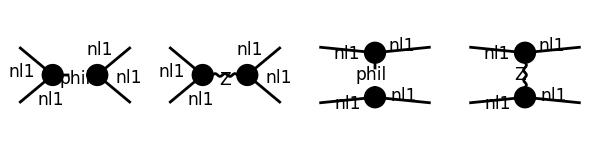

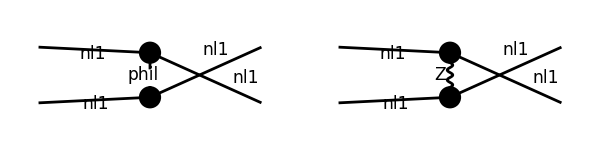

FeynArtsGraphics()(([] | [] | [] | []),([] | [] | Null | Null))

```mathematica
Paint[diagSI11,ColumnsXRows->{4,1},Numbering->None,SheetHeader->False,ImageSize->{600,150}]
```

```mathematica
pmnsmat = { PMNS1x1->0.8255,PMNS1x2->0.544521,PMNS1x3->0.1485,
		PMNS2x1->-0.454214,PMNS2x2->0.484741,PMNS2x3->0.747473,
		PMNS3x1->0.334031,PMNS3x2->-0.684487,PMNS3x3->0.647481};
couplings={FCGV["EL"]->√(4 π /137),sw->√0.231,cw->√(1-0.231)};

proprep={FeynAmpDenominator[PropagatorDenominator[Momentum[p_],mphi]]:>1/(SP[p]-mphi^2+ⅈ mphi Γphi),
		FeynAmpDenominator[PropagatorDenominator[-Momentum[p_],mphi]]:>1/(SP[p]-mphi^2+ⅈ mphi Γphi),
		FeynAmpDenominator[PropagatorDenominator[Momentum[p_],mZ]]:>(4 √2 GF cw^2 sw^2)/(FCGV["EL"])^2,
		FeynAmpDenominator[PropagatorDenominator[-Momentum[p_],mZ]]:>(4 √2 GF cw^2 sw^2)/(FCGV["EL"])^2};

kinemrep={Pair[Momentum[p1],Momentum[p2]]->1/2(s-2 mnlin^2),
		Pair[Momentum[p3],Momentum[p4]]->1/2(s-2 mnlout^2),
		Pair[Momentum[p1],Momentum[p3]]->-1/2(t-mnlin^2-mnlout^2),
		Pair[Momentum[p2],Momentum[p4]]->-1/2(t-mnlin^2-mnlout^2),
		Pair[Momentum[p1],Momentum[p4]]->-1/2(u-mnlin^2-mnlout^2),
		Pair[Momentum[p2],Momentum[p3]]->-1/2(u-mnlin^2-mnlout^2),
		Pair[Momentum[p3+p4],Momentum[p3+p4]]->s,
		Pair[Momentum[p2-p4],Momentum[p2-p4]]->t,
		Pair[Momentum[p2-p3],Momentum[p2-p3]]->u}/.{
t->-s/2+1/2(√(s-4 mnlin^2)√(s-4*mnlout^2)Cos[θ])+mnlin^2+mnlout^2,
u->-s/2-1/2(√(s-4 mnlin^2)√(s-4*mnlout^2)Cos[θ])+mnlin^2+mnlout^2}/.mnlin->0/.mnlout->0;
```

```mathematica
diagSIext[diag_,diagnum_]:=DiagramExtract[diag,diagnum]

RawAmpSI[diag_,diagnum_]:=
CreateFeynAmp[diagSIext[diag,diagnum]]/.{FeynAmpDenominator->FAFeynAmpDenominator,FeynAmpList->FAFeynAmpList,NonCommutative->FANonCommutative,PolarizationVector->FAPolarizationVector,DiracSpinor->Spinor}

FCampSI[diag_,diagnum_]:=DiracSimplify[FCFAConvert[RawAmpSI[diag,diagnum],List->False,DropSumOver->True,ChangeDimension->4,UndoChiralSplittings->True,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4}]]/.proprep

FAampSISq[diag_,diagnum1_,diagnum2_]:=DiracSimplify[FermionSpinSum[FCampSI[diag,diagnum1] ComplexConjugate[FCampSI[diag,diagnum2]]]]
```

```mathematica
(* Flavor Conserving Case *)

LOterm = FCampSI[diagSI11,2]+FCampSI[diagSI11,4]+FCampSI[diagSI11,6];
NPterm = FCampSI[diagSI11,1]+FCampSI[diagSI11,3]+FCampSI[diagSI11,5];

LOSMsq=DiracSimplify[FermionSpinSum[LOterm ComplexConjugate[LOterm]]]/.kinemrep//.pmnsmat//.couplings;
NPSMinterf=DiracSimplify[FermionSpinSum[LOterm ComplexConjugate[NPterm]+NPterm ComplexConjugate[LOterm]]]/.kinemrep//.pmnsmat//.couplings;
```

```mathematica
simplifiedInterf=Simplify[Normal[Series[Simplify[ComplexExpand[NPSMinterf]],{mnl1,0,2}]]/.Γphi->0.1mphi/.lphiN->0.01/.{mnl1->6 10^-7,mphi->0.1,mN1->10,GF->1.16 10^-11}];

fullSMNPTab=ParallelTable[{sqrts,(0.529112 GF^2 sqrts^2/.GF->1.16 10^-11)+1/(64 π^2 sqrts^2)(*Phase Space*)1/4(*Spin Av.*)2π (*ϕ Int*)NIntegrate[Sin[θ]simplifiedInterf/.s->sqrts^2,{θ,0,π}]},{sqrts,10^-4,10,0.01}];
tabtinterfPos=ParallelTable[{sqrts,1/(64 π^2 sqrts^2)(*Phase Space*)1/4(*Spin Av.*)2π (*ϕ Int*)NIntegrate[Sin[θ]simplifiedInterf/.s->sqrts^2,{θ,0,π}]},{sqrts,10^-4,0.1,0.01}];
tabtinterfNeg=ParallelTable[{sqrts,1/(64 π^2 sqrts^2)(*Phase Space*)1/4(*Spin Av.*)2π (*ϕ Int*)NIntegrate[Sin[θ]simplifiedInterf/.s->sqrts^2,{θ,0,π}]},{sqrts,0.1,10,0.01}];
```

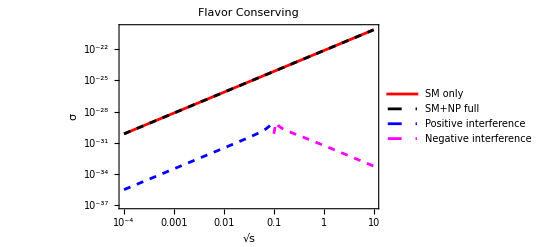

```mathematica
plot11=LogLogPlot[1/(64 π^2 s)(*Phase Space*)1/4(*Spin Av.*)2π (*ϕ Int*)Integrate[Sin[θ]LOSMsq//Simplify,{θ,0,π}]/.{mnl1->6 10^-7,mphi->0.1,mN1->10,GF->1.16 10^-11}/.s->sqrts^2//Simplify,{sqrts,10^-4,10},Frame->True,PlotRange->{10^-37,10^-20},PlotStyle->Red,PlotLegends->{"SM only"},FrameStyle->Black,FrameLabel->{"√s","σ"},PlotLabel->"Flavor Conserving",LabelStyle->Black,GridLines->Automatic];
plot22=ListLogLogPlot[fullSMNPTab,Joined->True,PlotStyle->Directive[Dashed,Black],PlotLegends->{"SM+NP full"}];
plot33=ListLogLogPlot[tabtinterfPos,Joined->True,PlotStyle->Directive[Dashed,Blue],PlotLegends->{"Positive interference"}];
plot44=ListLogLogPlot[Abs[tabtinterfNeg],Joined->True,PlotStyle->Directive[Dashed,Magenta],PlotLegends->{"Negative interference"}];
Show[plot11,plot22,plot33,plot44]
```

```mathematica
(* Flavor Changing Case *)

FCLOterm=FCampSI[diagSI12,2]+FCampSI[diagSI12,3]+FCampSI[diagSI12,4];
FCNPterm=FCampSI[diagSI12,1];
FCLOSMsq=DiracSimplify[FermionSpinSum[FCLOterm ComplexConjugate[FCLOterm]]]/.kinemrep//.pmnsmat//.couplings;
FCNPSMinterf=DiracSimplify[FermionSpinSum[FCLOterm ComplexConjugate[FCNPterm]+FCNPterm ComplexConjugate[FCLOterm]]]/.kinemrep//.pmnsmat//.couplings;
```

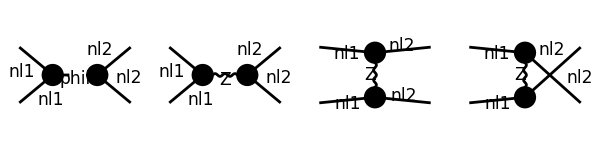

FeynArtsGraphics()(([] | [] | [] | []))

```mathematica
Paint[diagSI12,ColumnsXRows->{4,1},Numbering->None,SheetHeader->False,ImageSize->{600,150}]
```

```mathematica
simplifiedInterf=Simplify[Normal[Series[Simplify[ComplexExpand[FCNPSMinterf]],{mnl1,0,2}]]/.Γphi->0.1mphi/.lphiN->0.01/.{mnl1->6 10^-7,mnl2->3 10^-7,mphi->0.1,mN1->10,mN2->20,GF->1.16 10^-11}];

fullSMNPTab=ParallelTable[{sqrts,(0.0529813 GF^2 sqrts^2/.GF->1.16 10^-11)+1/(64 π^2 sqrts^2)(*Phase Space*)1/4(*Spin Av.*)2π (*ϕ Int*)NIntegrate[Sin[θ]simplifiedInterf/.s->sqrts^2,{θ,0,π}]},{sqrts,10^-4,10,0.01}];
tabtinterfPos=ParallelTable[{sqrts,1/(64 π^2 sqrts^2)(*Phase Space*)1/4(*Spin Av.*)2π (*ϕ Int*)NIntegrate[Sin[θ]simplifiedInterf/.s->sqrts^2,{θ,0,π}]},{sqrts,10^-4,0.1,0.01}];
tabtinterfNeg=ParallelTable[{sqrts,1/(64 π^2 sqrts^2)(*Phase Space*)1/4(*Spin Av.*)2π (*ϕ Int*)NIntegrate[Sin[θ]simplifiedInterf/.s->sqrts^2,{θ,0,π}]},{sqrts,0.1,10,0.01}];
```

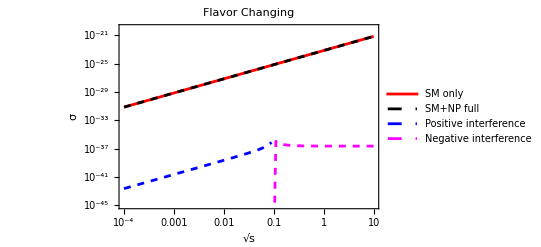

```mathematica
plot11=LogLogPlot[1/(64 π^2 s)(*Phase Space*)1/4(*Spin Av.*)2π (*ϕ Int*)Integrate[Sin[θ]FCLOSMsq//Simplify,{θ,0,π}]/.{mnl1->6 10^-7,mnl2->3 10^-7,mphi->0.1,mN1->10,mN2->20,GF->1.16 10^-11}/.s->sqrts^2//Simplify,{sqrts,10^-4,10},Frame->True,PlotRange->{10^-45,10^-20},PlotStyle->Red,PlotLegends->{"SM only"},FrameStyle->Black,FrameLabel->{"√s","σ"},PlotLabel->"Flavor Changing",LabelStyle->Black,GridLines->Automatic];
plot22=ListLogLogPlot[fullSMNPTab,Joined->True,PlotStyle->Directive[Dashed,Black],PlotLegends->{"SM+NP full"}];
plot33=ListLogLogPlot[tabtinterfPos,Joined->True,PlotStyle->Directive[Dashed,Blue],PlotLegends->{"Positive interference"}];
plot44=ListLogLogPlot[Abs[tabtinterfNeg],Joined->True,PlotStyle->Directive[Dashed,Magenta],PlotLegends->{"Negative interference"}];
Show[plot11,plot22,plot33,plot44]
```

#### Amplitudes e n_l → e n_l

```mathematica
topo=CreateTopologies[0,2->2];
diageveN[ii_]:=InsertFields[topo,{F[8],F[ii]}->{F[8],F[ii]},InsertionLevel->{Particles},Model->modelfile,GenericModel->modelfile]
```

```mathematica
(* light neutrino SI to heavy neutrino *)
diageveN11 = diageveN[1];
diageveN22 = diageveN[2];
diageveN33 = diageveN[3];

diageveN11 = DiagramDelete[diageveN11, {2}];
diageveN22 = DiagramDelete[diageveN22, {2}];
diageveN33 = DiagramDelete[diageveN33, {2}];
```

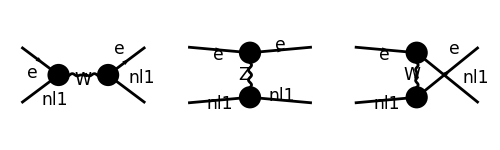

FeynArtsGraphics()(([] | [] | []))

```mathematica
Paint[diageveN11,ColumnsXRows->{3,1},Numbering->None,SheetHeader->False,ImageSize->{500,150}]
```

```mathematica
pmnsmat = { PMNS1x1->0.8255,PMNS1x2->0.544521,PMNS1x3->0.1485,
		PMNS2x1->-0.454214,PMNS2x2->0.484741,PMNS2x3->0.747473,
		PMNS3x1->0.334031,PMNS3x2->-0.684487,PMNS3x3->0.647481};
couplings={FCGV["EL"]->√(4 π /137),sw->√0.231,cw->√(1-0.231)};
massval={me->0.511 (*MeV*), mW->80369(*MeV*), mZ->91188(*MeV*)};

proprep={FeynAmpDenominator[PropagatorDenominator[Momentum[p_],mW]]:>1/(SP[p]-mW^2),
		FeynAmpDenominator[PropagatorDenominator[-Momentum[p_],mW]]:>1/(SP[p]-mW^2),
		FeynAmpDenominator[PropagatorDenominator[Momentum[p_],mZ]]:>1/(SP[p]-mZ^2),
		FeynAmpDenominator[PropagatorDenominator[-Momentum[p_],mZ]]:>1/(SP[p]-mZ^2)};
proprep={FeynAmpDenominator[PropagatorDenominator[Momentum[p_],mW]]:>1/-mW^2,
		FeynAmpDenominator[PropagatorDenominator[-Momentum[p_],mW]]:>1/-mW^2,
		FeynAmpDenominator[PropagatorDenominator[Momentum[p_],mZ]]:>1/-mZ^2,
		FeynAmpDenominator[PropagatorDenominator[-Momentum[p_],mZ]]:>1/-mZ^2};

kinemrep={Pair[Momentum[p1],Momentum[p2]]->1/2(s-m1v^2-m2v^2),
		Pair[Momentum[p3],Momentum[p4]]->1/2(s-m3v^2-m4v^2),
		Pair[Momentum[p1],Momentum[p3]]->-1/2(t-m1v^2-m3v^2),
		Pair[Momentum[p2],Momentum[p4]]->-1/2(t-m2v^2-m4v^2),
		Pair[Momentum[p1],Momentum[p4]]->-1/2(u-m1v^2-m4v^2),
		Pair[Momentum[p2],Momentum[p3]]->-1/2(u-m2v^2-m3v^2),
		Pair[Momentum[p3+p4],Momentum[p3+p4]]->s,
		Pair[Momentum[p2-p4],Momentum[p2-p4]]->t,
		Pair[Momentum[p2-p3],Momentum[p2-p3]]->u}/.{
t->-s/2+1/2(√(s-4 m2v^2)√(s-4 m4v^2)Cos[θ])+m2v^2+m4v^2,
u->-s/2-1/2(√(s-4 m2v^2)√(s-4 m3v^2)Cos[θ])+m2v^2+m3v^2}/.{m1v->me,m2v->mnlval,m3v->me,m4v->mnlval};
```

```mathematica
diagSIext[diag_,diagnum_]:=DiagramExtract[diag,diagnum]

RawAmpSI[diag_,diagnum_]:=
CreateFeynAmp[diagSIext[diag,diagnum]]/.{FeynAmpDenominator->FAFeynAmpDenominator,FeynAmpList->FAFeynAmpList,NonCommutative->FANonCommutative,PolarizationVector->FAPolarizationVector,DiracSpinor->Spinor}

FCampSI[diag_,diagnum_]:=DiracSimplify[FCFAConvert[RawAmpSI[diag,diagnum],List->False,DropSumOver->True,ChangeDimension->4,UndoChiralSplittings->True,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4}]]/.proprep

FAampSISq[diag_,diagnum1_,diagnum2_]:=DiracSimplify[FermionSpinSum[FCampSI[diag,diagnum1] ComplexConjugate[FCampSI[diag,diagnum2]]]]
```

```mathematica
intmed=FCampSI[diageveN11,1]+FCampSI[diageveN11,2]+FCampSI[diageveN11,3];
intmed2=DiracSimplify[FermionSpinSum[intmed ComplexConjugate[intmed]]];
```

```mathematica
test123=intmed2/.kinemrep/.pmnsmat/.couplings/.massval/.{mnlval->mnl1,mnhval->mN1}//.{mnl1->3 10^-8,mnl2->3 10^-8,mnl3->3 10^-8,mN1->10,mN2->10,mN3->10}//Simplify;
```

```mathematica
tempo1=intmed2/.kinemrep/.pmnsmat/.couplings/.massval//Simplify;
```

```mathematica
xxx=1/(64 π^2 s)1/4 2π  Integrate[Sin[θ]test123,{θ,0,π}]//Simplify
```

5.57366×10^-24 s+(2.85027×10^-25)/s-3.48522×10^-24

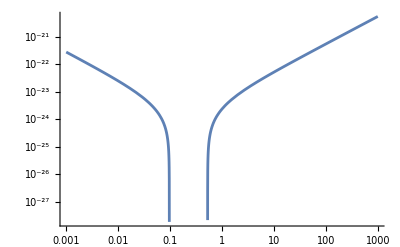

```mathematica
LogLogPlot[xxx,{s,1*^-3,1*^3}]
```

```mathematica
tempo1p=tempo1/.{mnlval->mnl1,mnhval->mN1}//.{mnl1->3 10^-8,mnl2->3 10^-8,mnl3->3 10^-8,mN1->10,mN2->10,mN3->10}//Simplify;
```

```mathematica
intmedSM=ParallelTable[{ii,1/(64 π^2 ii^2)(√(ii^2)/2)/(ii/2)(*Phase Space*)1/4(*Spin Av.*)2π  NIntegrate[Sin[θ]tempo1p/.s->ii^2,{θ,0,π}]},{ii,0.52,1000,1}];
```

```mathematica
approx123=ParallelTable[{ii,1/(64 π^2 ii^2)(√(ii^2)/2)/(ii/2)(*Phase Space*)1/4(*Spin Av.*)2π  NIntegrate[Sin[θ]test123/.{mnlval->mnl1,mnhval->mN1}//.{mnl1->3 10^-8,mnl2->3 10^-8,mnl3->3 10^-8,mN1->10,mN2->10,mN3->10}/.s->ii^2,{θ,0,π}]},{ii,20.001,1000,1}];
```

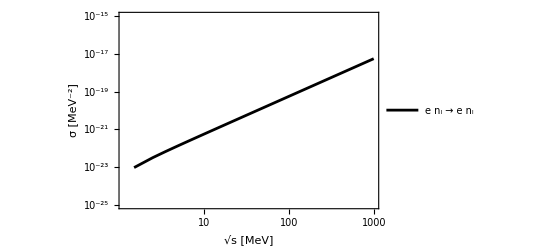

```mathematica
Show[ListLogLogPlot[intmedSM,Joined->True,PlotStyle->Directive[Black],PlotLegends->{"e n_l → e n_l"},Frame->True,FrameLabel->{"√s [MeV]","σ  [MeV^-2]"},FrameStyle->Black,GridLines->Automatic,PlotRange->{10^-25,10^-15}]]
```

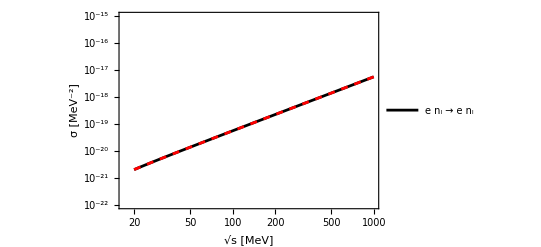

```mathematica
Show[ListLogLogPlot[{intmedSM, approx123},Joined->True,PlotStyle->{Directive[Black], Directive[Dashed,Red]},PlotLegends->{"e n_l → e n_l"},Frame->True,FrameLabel->{"√s [MeV]","σ  [MeV^-2]"},FrameStyle->Black,GridLines->Automatic,PlotRange->{10^-22,10^-15}]]
```

```mathematica
(*Show[LogLogPlot[intmed4/.s->sqrts^2,{sqrts,2 10,1000},PlotStyle->Directive[Dashed,Gray],PlotRange->All,PlotLegends->{"2 n_l → 2 n_h"},Frame->True,FrameLabel->{"√s [MeV]","σ  [MeV^-2]"},FrameStyle->Black,GridLines->Automatic],LogLogPlot[test2/.s->sqrts^2,{sqrts,2 10,1000},PlotStyle->Black,PlotLegends->{"2 n_l → 2 n_l"}]]*)
```

#### Amplitudes e n_l → e n_h

```mathematica
topo=CreateTopologies[0,2->2];
diageveN[ii_,jj_]:=InsertFields[topo,{F[8],F[ii]}->{F[8],F[jj]},InsertionLevel->{Particles},Model->modelfile,GenericModel->modelfile]
```

```mathematica
(* light neutrino SI to heavy neutrino *)
diageveN11 = diageveN[1,4];
diageveN22 = diageveN[2,5];
diageveN33 = diageveN[3,6];

diageveN11 = DiagramDelete[diageveN11, {2}];
diageveN22 = DiagramDelete[diageveN22, {2}];
diageveN33 = DiagramDelete[diageveN33, {2}];
```

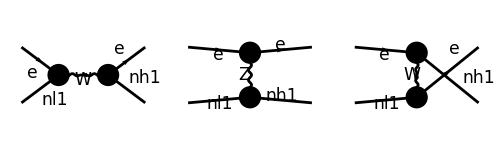

FeynArtsGraphics()(([] | [] | []))

```mathematica
Paint[diageveN11,ColumnsXRows->{3,1},Numbering->None,SheetHeader->False,ImageSize->{500,150}]
```

```mathematica
pmnsmat = { PMNS1x1->0.8255,PMNS1x2->0.544521,PMNS1x3->0.1485,
		PMNS2x1->-0.454214,PMNS2x2->0.484741,PMNS2x3->0.747473,
		PMNS3x1->0.334031,PMNS3x2->-0.684487,PMNS3x3->0.647481};
couplings={FCGV["EL"]->√(4 π /137),sw->√0.231,cw->√(1-0.231)};
massval={me->0.511 (*MeV*), mW->80369(*MeV*), mZ->91188(*MeV*)};

proprep={FeynAmpDenominator[PropagatorDenominator[Momentum[p_],mW]]:>1/(SP[p]-mW^2),
		FeynAmpDenominator[PropagatorDenominator[-Momentum[p_],mW]]:>1/(SP[p]-mW^2),
		FeynAmpDenominator[PropagatorDenominator[Momentum[p_],mZ]]:>1/(SP[p]-mZ^2),
		FeynAmpDenominator[PropagatorDenominator[-Momentum[p_],mZ]]:>1/(SP[p]-mZ^2)};

proprep={FeynAmpDenominator[PropagatorDenominator[Momentum[p_],mW]]:>1/-mW^2,
		FeynAmpDenominator[PropagatorDenominator[-Momentum[p_],mW]]:>1/-mW^2,
		FeynAmpDenominator[PropagatorDenominator[Momentum[p_],mZ]]:>1/-mZ^2,
		FeynAmpDenominator[PropagatorDenominator[-Momentum[p_],mZ]]:>1/-mZ^2};

kinemrep={Pair[Momentum[p1],Momentum[p2]]->1/2(s-m1v^2-m2v^2),
		Pair[Momentum[p3],Momentum[p4]]->1/2(s-m3v^2-m4v^2),
		Pair[Momentum[p1],Momentum[p3]]->-1/2(t-m1v^2-m3v^2),
		Pair[Momentum[p2],Momentum[p4]]->-1/2(t-m2v^2-m4v^2),
		Pair[Momentum[p1],Momentum[p4]]->-1/2(u-m1v^2-m4v^2),
		Pair[Momentum[p2],Momentum[p3]]->-1/2(u-m2v^2-m3v^2),
		Pair[Momentum[p3+p4],Momentum[p3+p4]]->s,
		Pair[Momentum[p2-p4],Momentum[p2-p4]]->t,
		Pair[Momentum[p2-p3],Momentum[p2-p3]]->u}/.{
t->-s/2+1/2(√(s-4 m2v^2)√(s-4 m4v^2)Cos[θ])+m2v^2+m4v^2,
u->-s/2-1/2(√(s-4 m2v^2)√(s-4 m3v^2)Cos[θ])+m2v^2+m3v^2}/.{m1v->me,m2v->mnlval,m3v->me,m4v->mnhval};
```

```mathematica
diagSIext[diag_,diagnum_]:=DiagramExtract[diag,diagnum]

RawAmpSI[diag_,diagnum_]:=
CreateFeynAmp[diagSIext[diag,diagnum]]/.{FeynAmpDenominator->FAFeynAmpDenominator,FeynAmpList->FAFeynAmpList,NonCommutative->FANonCommutative,PolarizationVector->FAPolarizationVector,DiracSpinor->Spinor}

FCampSI[diag_,diagnum_]:=DiracSimplify[FCFAConvert[RawAmpSI[diag,diagnum],List->False,DropSumOver->True,ChangeDimension->4,UndoChiralSplittings->True,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4}]]/.proprep

FAampSISq[diag_,diagnum1_,diagnum2_]:=DiracSimplify[FermionSpinSum[FCampSI[diag,diagnum1] ComplexConjugate[FCampSI[diag,diagnum2]]]]
```

```mathematica
intmed=FCampSI[diageveN11,1]+FCampSI[diageveN11,2]+FCampSI[diageveN11,3];
intmed2=DiracSimplify[FermionSpinSum[intmed ComplexConjugate[intmed]]];
```

```mathematica
tempo1=intmed2/.kinemrep/.pmnsmat/.couplings/.massval//Simplify;
```

```mathematica
tempo1p=tempo1/.{mnlval->mnl1,mnhval->mN1}//.{mnl1->3 10^-8,mnl2->3 10^-8,mnl3->3 10^-8,mN1->10,mN2->10,mN3->10}//Simplify;
```

```mathematica
intmedFCnh=ParallelTable[{ii,1/(64 π^2 ii^2)(√(ii^2-10^2)/2)/(ii/2)(*Phase Space*)1/4(*Spin Av.*)2π  NIntegrate[Sin[θ]tempo1p/.s->ii^2,{θ,0,π}]},{ii,10.001,1000,1}];
```

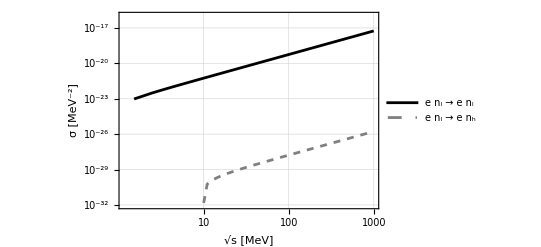

```mathematica
Show[ListLogLogPlot[{intmedSM,intmedFCnh},Joined->True,PlotStyle->{Black,Directive[Dashed,Gray]},PlotLegends->{"e n_l → e n_l","e n_l → e n_h"},Frame->True,FrameLabel->{"√s [MeV]","σ  [MeV^-2]"},FrameStyle->Black,GridLines->Automatic,PlotRange->{10^-32,10^-16}]]
```

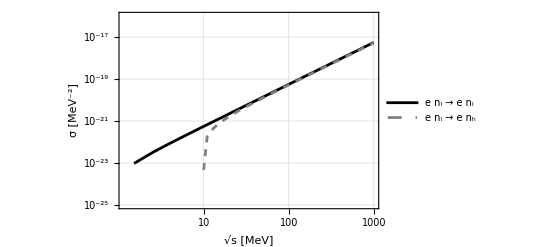

```mathematica
Show[ListLogLogPlot[{intmedSM,Transpose[{intmedFCnh[[;;,1]],10^8.5 intmedFCnh[[;;,2]]}]},Joined->True,PlotStyle->{Black,Directive[Dashed,Gray]},PlotLegends->{"e n_l → e n_l","e n_l → e n_h"},Frame->True,FrameLabel->{"√s [MeV]","σ  [MeV^-2]"},FrameStyle->Black,GridLines->Automatic,PlotRange->{10^-25,10^-16}]]
```

```mathematica
(*Show[LogLogPlot[intmed4/.s->sqrts^2,{sqrts,2 10,1000},PlotStyle->Directive[Dashed,Gray],PlotRange->All,PlotLegends->{"2 n_l → 2 n_h"},Frame->True,FrameLabel->{"√s [MeV]","σ  [MeV^-2]"},FrameStyle->Black,GridLines->Automatic],LogLogPlot[test2/.s->sqrts^2,{sqrts,2 10,1000},PlotStyle->Black,PlotLegends->{"2 n_l → 2 n_l"}]]*)
```

#### Amplitudes n_l n_l → n_l n_h

```mathematica
topo=CreateTopologies[0,2->2];
diagSI[ii_,jj_]:=InsertFields[topo,{F[ii],F[ii]}->{F[ii],F[jj]},InsertionLevel->{Particles},Model->modelfile,GenericModel->modelfile]
```

```mathematica
(* light neutrino SI to heavy neutrino *)
diagSI11 = diagSI[1,4];
diagSI22 = diagSI[2,5];
diagSI33 = diagSI[3,6];

diagSI11 = DiagramDelete[diagSI11, {1,4,7}];
diagSI22 = DiagramDelete[diagSI22,  {1,4,7}];
diagSI33 = DiagramDelete[diagSI33,  {1,4,7}];
```

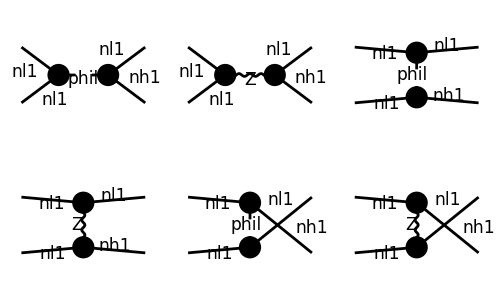

FeynArtsGraphics()(([] | [] | []
[] | [] | []))

```mathematica
Paint[diagSI11,ColumnsXRows->{3,2},Numbering->None,SheetHeader->False,ImageSize->{500,300}]
```

```mathematica
pmnsmat = { PMNS1x1->0.8255,PMNS1x2->0.544521,PMNS1x3->0.1485,
		PMNS2x1->-0.454214,PMNS2x2->0.484741,PMNS2x3->0.747473,
		PMNS3x1->0.334031,PMNS3x2->-0.684487,PMNS3x3->0.647481};
couplings={FCGV["EL"]->√(4 π /137),sw->√0.231,cw->√(1-0.231)};
massval={me->0.511 (*MeV*), mW->80369(*MeV*), mZ->91188(*MeV*)};

proprep={FeynAmpDenominator[PropagatorDenominator[Momentum[p_],mW]]:>1/(SP[p]-mW^2),
		FeynAmpDenominator[PropagatorDenominator[-Momentum[p_],mW]]:>1/(SP[p]-mW^2),
		FeynAmpDenominator[PropagatorDenominator[Momentum[p_],mZ]]:>1/(SP[p]-mZ^2),
		FeynAmpDenominator[PropagatorDenominator[-Momentum[p_],mZ]]:>1/(SP[p]-mZ^2)};

proprep={FeynAmpDenominator[PropagatorDenominator[Momentum[p_],mW]]:>1/-mW^2,
		FeynAmpDenominator[PropagatorDenominator[-Momentum[p_],mW]]:>1/-mW^2,
		FeynAmpDenominator[PropagatorDenominator[Momentum[p_],mZ]]:>1/-mZ^2,
		FeynAmpDenominator[PropagatorDenominator[-Momentum[p_],mZ]]:>1/-mZ^2,
		FeynAmpDenominator[PropagatorDenominator[Momentum[p_],mphi]]:>1/(SP[p]-mphi^2(*+ⅈ mphi Γphi*)),
		FeynAmpDenominator[PropagatorDenominator[-Momentum[p_],mphi]]:>1/(SP[p]-mphi^2(*+ⅈ mphi Γphi*))};

kinemrep={Pair[Momentum[p1],Momentum[p2]]->1/2(s-m1v^2-m2v^2),
		Pair[Momentum[p3],Momentum[p4]]->1/2(s-m3v^2-m4v^2),
		Pair[Momentum[p1],Momentum[p3]]->-1/2(t-m1v^2-m3v^2),
		Pair[Momentum[p2],Momentum[p4]]->-1/2(t-m2v^2-m4v^2),
		Pair[Momentum[p1],Momentum[p4]]->-1/2(u-m1v^2-m4v^2),
		Pair[Momentum[p2],Momentum[p3]]->-1/2(u-m2v^2-m3v^2),
		Pair[Momentum[p3+p4],Momentum[p3+p4]]->s,
		Pair[Momentum[p2-p4],Momentum[p2-p4]]->t,
		Pair[Momentum[p2-p3],Momentum[p2-p3]]->u}/.{
t->-s/2+1/2(√(s-4 m2v^2)√(s-4 m4v^2)Cos[θ])+m2v^2+m4v^2,
u->-s/2-1/2(√(s-4 m2v^2)√(s-4 m3v^2)Cos[θ])+m2v^2+m3v^2}/.{m1v->mnlval,m2v->mnlval,m3v->mnlval,m4v->mnhval};
```

```mathematica
diagSIext[diag_,diagnum_]:=DiagramExtract[diag,diagnum]

RawAmpSI[diag_,diagnum_]:=
CreateFeynAmp[diagSIext[diag,diagnum]]/.{FeynAmpDenominator->FAFeynAmpDenominator,FeynAmpList->FAFeynAmpList,NonCommutative->FANonCommutative,PolarizationVector->FAPolarizationVector,DiracSpinor->Spinor}

FCampSI[diag_,diagnum_]:=DiracSimplify[FCFAConvert[RawAmpSI[diag,diagnum],List->False,DropSumOver->True,ChangeDimension->4,UndoChiralSplittings->True,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4}]]/.proprep

FAampSISq[diag_,diagnum1_,diagnum2_]:=DiracSimplify[FermionSpinSum[FCampSI[diag,diagnum1] ComplexConjugate[FCampSI[diag,diagnum2]]]]
```

```mathematica
intmed=FCampSI[diagSI11,1]+FCampSI[diagSI11,2]+FCampSI[diagSI11,3]+FCampSI[diagSI11,4]+FCampSI[diagSI11,5]+FCampSI[diagSI11,6]//Simplify;
intmed2=DiracSimplify[FermionSpinSum[intmed ComplexConjugate[intmed]]];
```

```mathematica
tempo=intmed2/.kinemrep//.pmnsmat//.couplings/.{mphi->0,mnlval->mnl1,mnhval->mN1};
```

```mathematica
tempo2=Normal[Series[Normal[Series[Normal[Series[tempo,{mnl1,0,2}]],{mnl2,0,0}]],{mnl3,0,0}]];
```

```mathematica
tempo33=tempo2//.{mnl1->3 10^-8,mnl2->3 10^-8,mnl3->3 10^-8,mN1->10,mN2->10,mN3->10,lphiN->0.1,mphi->0.}/.massval;
```

```mathematica
1/(64 π^2 s)1/4(*Spin Av.*)2π Integrate[Sin[θ]tempo33,{θ,0,π}]//Simplify
```

8.89434×10^-32 s-(1.51434×10^-29)/s-7.11547×10^-30

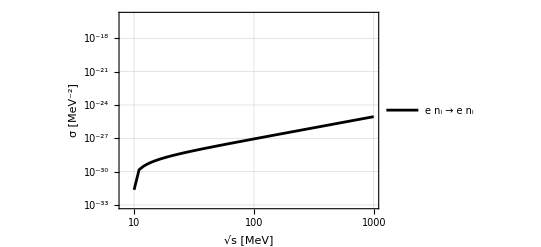

```mathematica
tempo44=ParallelTable[{ii,1/(64 π^2 ii^2)(√(ii^2-10^2)/2)/(ii/2)(*Phase Space*)1/4(*Spin Av.*)2π  Quiet[NIntegrate[Sin[θ]tempo33/.s->ii^2,{θ,0,π}]]},{ii,10.001,10^3,1}];
ListLogLogPlot[{tempo44},Joined->True,PlotStyle->{Black,Directive[Gray,Dashed],Red},PlotLegends->{"e n_l → e n_l","e n_l → e n_h", "n_l n_l → n_h n_h"},Frame->True,FrameLabel->{"√s [MeV]","σ  [MeV^-2]"},FrameStyle->Black,GridLines->Automatic,PlotRange->{10^-33,10^-16}]
```

```mathematica
tempo3=tempo2/.{
t->-s/2+1/2(√(s-4 mnlin^2)√(s-4*mnlout^2)Cos[θ])+mnlin^2+mnlout^2,
u->-s/2-1/2(√(s-4 mnlin^2)√(s-4*mnlout^2)Cos[θ])+mnlin^2+mnlout^2}/.mnlin->mnl1/.mnlout->mN1//.{mnl1->3 10^-8,mnl2->3 10^-8,mnl3->3 10^-8,mN1->10,mN2->10,mN3->10,lphiN->0.1,mphi->0.}/.massval/.s->sqrts^2;
```

```mathematica
tempo4=ParallelTable[{ii,1/(64 π^2 ii^2)(√(ii^2-20^2)/2)/(ii/2)(*Phase Space*)1/4(*Spin Av.*)2π  Quiet[NIntegrate[Sin[θ]tempo3/.sqrts->ii,{θ,0,π}]]},{ii,20.001,10^3,1}];
```

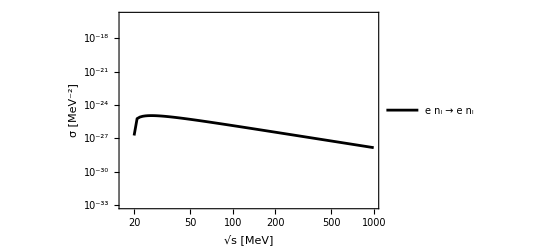

```mathematica
ListLogLogPlot[{tempo4},Joined->True,PlotStyle->{Black,Directive[Gray],Red},PlotLegends->{"e n_l → e n_l","e n_l → e n_h", "n_l n_l → n_h n_h"},Frame->True,FrameLabel->{"√s [MeV]","σ  [MeV^-2]"},FrameStyle->Black,GridLines->Automatic,PlotRange->{10^-33,10^-16}]
```

```mathematica
intmed22=intmed2/.s->sqrts^2//Simplify;

intmed222=ParallelTable[{ii,1/(64 π^2 ii^2)(√(ii^2-20^2)/2)/(ii/2)(*Phase Space*)1/4(*Spin Av.*)2π  Quiet[NIntegrate[Sin[θ]intmed22/.sqrts->ii,{θ,0,π}]]},{ii,20.001,10^3,1}];
```

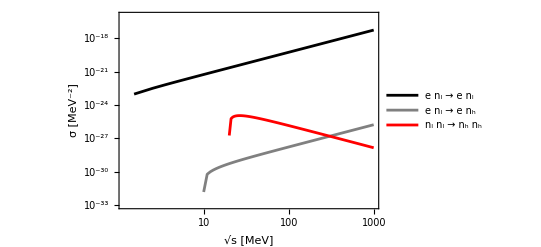

```mathematica
Show[ListLogLogPlot[{intmedSM,intmedFCnh,intmed222},Joined->True,PlotStyle->{Black,Directive[Gray],Red},PlotLegends->{"e n_l → e n_l","e n_l → e n_h", "n_l n_l → n_h n_h"},Frame->True,FrameLabel->{"√s [MeV]","σ  [MeV^-2]"},FrameStyle->Black,GridLines->Automatic,PlotRange->{10^-33,10^-16}]]
```

```mathematica
(*tett=ParallelTable[{ii,(√(ii^2-20^2))/(√(ii^2))10^-22 ii^-2},{ii,20.001,1000,1}];
Show[ListLogLogPlot[{intmedSM,tett,intmed222},Joined->True,PlotStyle->{Black,Directive[Gray],Red},PlotLegends->{"e n_l → e n_l","e n_l → e n_h", "n_l n_l → n_h n_h"},Frame->True,FrameLabel->{"√s [MeV]","σ  [MeV^-2]"},FrameStyle->Black,GridLines->Automatic,PlotRange->{10^-33,10^-16}]]*)
```

```mathematica
(*
intmed=FCampSI[diagSI11,2]+FCampSI[diagSI11,3];
intmed2=DiracSimplify[FermionSpinSum[intmed ComplexConjugate[intmed]]];
intmed2=intmed2/.kinemrep//.pmnsmat//.couplings/.{mnlin->mnl1,mnlout->mN1}//Simplify;

intmed22=intmed2/.{mnl1->6 10^-7,mN1->10,mphi->0.1,Γphi->0.01,lphiN->0.01}/.s->sqrts^2//Simplify;

intmed222=ParallelTable[{ii,1/(64 π^2 ii^2)(√(ii^2-20^2)/2)/(ii/2)(*Phase Space*)1/4(*Spin Av.*)2π  NIntegrate[Sin[θ]intmed22/.sqrts->ii,{θ,0,π}]},{ii,20.001,1000,1}];
*)
(*intmed2int=Integrate[Sin[θ]intmed2,{θ,0,π}];
intmed3=1/(64 π^2 s)(*Phase Space*)1/4(*Spin Av.*)2π intmed2int;
Export["~/Desktop/N_effective/Type_I_variant/nlnl2nhnh.wdx",intmed3];*)

(*intmed4=Import["~/Desktop/N_effective/Type_I_variant/nlnl2nhnh.wdx"]/.{mnl1->6 10^-7,mN1->10,mphi->0.1,Γphi->0.01,lphiN->0.01};*)
(*
intmed222full = intmed222;
intmed222nos=intmed222;

Show[ListLogLogPlot[intmed222full,Joined->True,PlotStyle->Directive[Dashed,Black],PlotLegends->{"full"},Frame->True,FrameLabel->{"√s [MeV]","σ  [MeV^-2]"},FrameStyle->Black,GridLines->Automatic,PlotRange->{10^-29,10^-18}],ListLogLogPlot[intmed222nos,Joined->True,PlotStyle->Directive[Dashed,Gray],PlotLegends->{"s-channel removed"},Frame->True,FrameLabel->{"√s [MeV]","σ  [MeV^-2]"},FrameStyle->Black,GridLines->Automatic,PlotRange->{10^-29,10^-18}]]
*)
```

```mathematica
(*Show[LogLogPlot[intmed4/.s->sqrts^2,{sqrts,2 10,1000},PlotStyle->Directive[Dashed,Gray],PlotRange->All,PlotLegends->{"2 n_l → 2 n_h"},Frame->True,FrameLabel->{"√s [MeV]","σ  [MeV^-2]"},FrameStyle->Black,GridLines->Automatic],LogLogPlot[test2/.s->sqrts^2,{sqrts,2 10,1000},PlotStyle->Black,PlotLegends->{"2 n_l → 2 n_l"}]]*)
```

#### Amplitudes n_l n_l → n_h n_h

```mathematica
topo=CreateTopologies[0,2->2];
diagSI[ii_,jj_]:=InsertFields[topo,{F[ii],F[ii]}->{F[jj],F[jj]},InsertionLevel->{Particles},Model->modelfile,GenericModel->modelfile]
```

```mathematica
(* light neutrino SI to heavy neutrino *)
diagSI11 = diagSI[1,4];
diagSI22 = diagSI[2,5];
diagSI33 = diagSI[3,6];

diagSI11 = DiagramDelete[diagSI11, {1,4,7}];
diagSI22 = DiagramDelete[diagSI22,  {1,4,7}];
diagSI33 = DiagramDelete[diagSI33,  {1,4,7}];
```

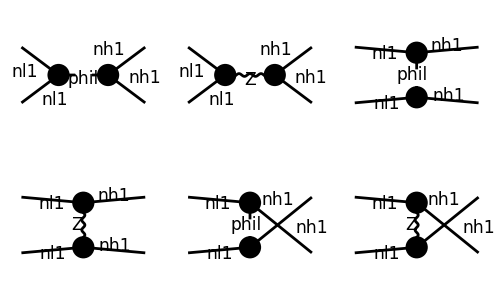

FeynArtsGraphics()(([] | [] | []
[] | [] | []))

```mathematica
Paint[diagSI11,ColumnsXRows->{3,2},Numbering->None,SheetHeader->False,ImageSize->{500,300}]
```

```mathematica
pmnsmat = { PMNS1x1->0.8255,PMNS1x2->0.544521,PMNS1x3->0.1485,
		PMNS2x1->-0.454214,PMNS2x2->0.484741,PMNS2x3->0.747473,
		PMNS3x1->0.334031,PMNS3x2->-0.684487,PMNS3x3->0.647481};
couplings={FCGV["EL"]->√(4 π /137),sw->√0.231,cw->√(1-0.231)};
massval={me->0.511 (*MeV*), mW->80369(*MeV*), mZ->91188(*MeV*)};

proprep={FeynAmpDenominator[PropagatorDenominator[Momentum[p_],mphi]]:>1/(SP[p]-mphi^2(*+ⅈ mphi Γphi*)),
		FeynAmpDenominator[PropagatorDenominator[-Momentum[p_],mphi]]:>1/(SP[p]-mphi^2(*+ⅈ mphi Γphi*)),
		FeynAmpDenominator[PropagatorDenominator[Momentum[p_],mZ]]:>1/(SP[p]-mZ^2),
		FeynAmpDenominator[PropagatorDenominator[-Momentum[p_],mZ]]:>1/(SP[p]-mZ^2)};
proprep={FeynAmpDenominator[PropagatorDenominator[Momentum[p_],mphi]]:>1/(SP[p]-mphi^2(*+ⅈ mphi Γphi*)),
		FeynAmpDenominator[PropagatorDenominator[-Momentum[p_],mphi]]:>1/(SP[p]-mphi^2(*+ⅈ mphi Γphi*)),
		FeynAmpDenominator[PropagatorDenominator[Momentum[p_],mZ]]:>1/-mZ^2,
		FeynAmpDenominator[PropagatorDenominator[-Momentum[p_],mZ]]:>1/-mZ^2};

kinemrep={Pair[Momentum[p1],Momentum[p2]]->1/2(s-2 mnlin^2),
		Pair[Momentum[p3],Momentum[p4]]->1/2(s-2 mnlout^2),
		Pair[Momentum[p1],Momentum[p3]]->-1/2(t-mnlin^2-mnlout^2),
		Pair[Momentum[p2],Momentum[p4]]->-1/2(t-mnlin^2-mnlout^2),
		Pair[Momentum[p1],Momentum[p4]]->-1/2(u-mnlin^2-mnlout^2),
		Pair[Momentum[p2],Momentum[p3]]->-1/2(u-mnlin^2-mnlout^2),
		Pair[Momentum[p3+p4],Momentum[p3+p4]]->s,
		Pair[Momentum[p2-p4],Momentum[p2-p4]]->t,
		Pair[Momentum[p2-p3],Momentum[p2-p3]]->u}(*/.{
t->-s/2+1/2(√(s-4 mnlin^2)√(s-4*mnlout^2)Cos[θ])+mnlin^2+mnlout^2,
u->-s/2-1/2(√(s-4 mnlin^2)√(s-4*mnlout^2)Cos[θ])+mnlin^2+mnlout^2}*)/.mnlin->mnl1/.mnlout->mN1;
```

```mathematica
diagSIext[diag_,diagnum_]:=DiagramExtract[diag,diagnum]

RawAmpSI[diag_,diagnum_]:=
CreateFeynAmp[diagSIext[diag,diagnum]]/.{FeynAmpDenominator->FAFeynAmpDenominator,FeynAmpList->FAFeynAmpList,NonCommutative->FANonCommutative,PolarizationVector->FAPolarizationVector,DiracSpinor->Spinor}

FCampSI[diag_,diagnum_]:=DiracSimplify[FCFAConvert[RawAmpSI[diag,diagnum],List->False,DropSumOver->True,ChangeDimension->4,UndoChiralSplittings->True,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4}]]/.proprep

FAampSISq[diag_,diagnum1_,diagnum2_]:=DiracSimplify[FermionSpinSum[FCampSI[diag,diagnum1] ComplexConjugate[FCampSI[diag,diagnum2]]]]
```

```mathematica
intmed=FCampSI[diagSI11,1]+FCampSI[diagSI11,2]+FCampSI[diagSI11,3]+FCampSI[diagSI11,4]+FCampSI[diagSI11,5]+FCampSI[diagSI11,6]//Simplify;
intmed2=DiracSimplify[FermionSpinSum[intmed ComplexConjugate[intmed]]];
```

```mathematica
tempo=intmed2/.kinemrep//.pmnsmat//.couplings/.{mnlin->mnl1,mnlout->mN1};
```

```mathematica
tempo2=Normal[Series[Normal[Series[Normal[Series[tempo,{mnl1,0,2}]],{mnl2,0,0}]],{mnl3,0,0}]];
```

```mathematica
tempo33=SeriesCoefficient[tempo2/.mphi->0//Chop//Expand,{lphiN,0,4}] lphiN^4/.{
t->-s/2+1/2(√(s-4 mnlin^2)√(s-4*mnlout^2)Cos[θ])+mnlin^2+mnlout^2,
u->-s/2-1/2(√(s-4 mnlin^2)√(s-4*mnlout^2)Cos[θ])+mnlin^2+mnlout^2}/.mnlin->mnl1/.mnlout->mN1//.{mnl1->3 10^-8,mnl2->3 10^-8,mnl3->3 10^-8,mN1->10,mN2->10,mN3->10,lphiN->0.1,mphi->0.}/.massval/.s->sqrts^2;
```

```mathematica
SeriesCoefficient[mN1^2/(4 mnl1^2)tempo2/.mphi->0//Chop//Expand,{lphiN,0,4}]
```

(1. mN1^4)/t^2-(1. mN1^4)/(t u)+(1. mN1^4)/u^2-(1. mN1^2 u)/(s t)-(1. mN1^2 t)/(s u)-(2. mN1^2 s)/(t u)-(2. mN1^2)/s+(1. mN1^2)/t+(1. mN1^2)/u+(0.5 s^2)/(t u)+(0.5 t^2)/(s u)+(0.5 u^2)/(s t)-(0.5 t)/s-(0.5 s)/t-(0.5 u)/s-(0.5 s)/u-(0.5 u)/t-(0.5 t)/u+3.

```mathematica
SeriesCoefficient[mN1^2/(4 mnl1^2)tempo2/.mphi->0//Chop//Expand,{lphiN,0,4}] lphiN^4(*mnl1^2/mN1^2*)
```

lphiN^4 ((1. mN1^4)/t^2-(1. mN1^4)/(t u)+(1. mN1^4)/u^2-(1. mN1^2 u)/(s t)-(1. mN1^2 t)/(s u)-(2. mN1^2 s)/(t u)-(2. mN1^2)/s+(1. mN1^2)/t+(1. mN1^2)/u+(0.5 s^2)/(t u)+(0.5 t^2)/(s u)+(0.5 u^2)/(s t)-(0.5 t)/s-(0.5 s)/t-(0.5 u)/s-(0.5 s)/u-(0.5 u)/t-(0.5 t)/u+3.)

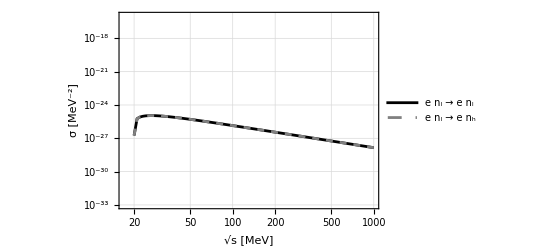

```mathematica
tempo44=ParallelTable[{ii,1/(64 π^2 ii^2)(√(ii^2-20^2)/2)/(ii/2)(*Phase Space*)1/4(*Spin Av.*)2π  Quiet[NIntegrate[Sin[θ]tempo33/.sqrts->ii,{θ,0,π}]]},{ii,20.001,10^3,1}];
ListLogLogPlot[{tempo4,tempo44},Joined->True,PlotStyle->{Black,Directive[Gray,Dashed],Red},PlotLegends->{"e n_l → e n_l","e n_l → e n_h", "n_l n_l → n_h n_h"},Frame->True,FrameLabel->{"√s [MeV]","σ  [MeV^-2]"},FrameStyle->Black,GridLines->Automatic,PlotRange->{10^-33,10^-16}]
```

```mathematica
tempo3=tempo2/.{
t->-s/2+1/2(√(s-4 mnlin^2)√(s-4*mnlout^2)Cos[θ])+mnlin^2+mnlout^2,
u->-s/2-1/2(√(s-4 mnlin^2)√(s-4*mnlout^2)Cos[θ])+mnlin^2+mnlout^2}/.mnlin->mnl1/.mnlout->mN1//.{mnl1->3 10^-8,mnl2->3 10^-8,mnl3->3 10^-8,mN1->10,mN2->10,mN3->10,lphiN->0.1,mphi->0.}/.massval/.s->sqrts^2;
```

```mathematica
tempo4=ParallelTable[{ii,1/(64 π^2 ii^2)(√(ii^2-20^2)/2)/(ii/2)(*Phase Space*)1/4(*Spin Av.*)2π  Quiet[NIntegrate[Sin[θ]tempo3/.sqrts->ii,{θ,0,π}]]},{ii,20.001,10^3,1}];
```

```mathematica
ListLogLogPlot[{tempo4},Joined->True,PlotStyle->{Black,Directive[Gray],Red},PlotLegends->{"e n_l → e n_l","e n_l → e n_h", "n_l n_l → n_h n_h"},Frame->True,FrameLabel->{"√s [MeV]","σ  [MeV^-2]"},FrameStyle->Black,GridLines->Automatic,PlotRange->{10^-33,10^-16}]
```

-Graphics-

```mathematica
intmed2=intmed2/.kinemrep//.pmnsmat//.couplings/.{mnlin->mnl1,mnlout->mN1}//.{mnl1->3 10^-8,mnl2->3 10^-8,mnl3->3 10^-8,mN1->10,mN2->10,mN3->10,lphiN->0.1,mphi->0.03}/.massval;
```

```mathematica
intmed22=intmed2/.s->sqrts^2//Simplify;

intmed222=ParallelTable[{ii,1/(64 π^2 ii^2)(√(ii^2-20^2)/2)/(ii/2)(*Phase Space*)1/4(*Spin Av.*)2π  Quiet[NIntegrate[Sin[θ]intmed22/.sqrts->ii,{θ,0,π}]]},{ii,20.001,10^3,1}];
```

```mathematica
Show[ListLogLogPlot[{intmedSM,intmedFCnh,intmed222},Joined->True,PlotStyle->{Black,Directive[Gray],Red},PlotLegends->{"e n_l → e n_l","e n_l → e n_h", "n_l n_l → n_h n_h"},Frame->True,FrameLabel->{"√s [MeV]","σ  [MeV^-2]"},FrameStyle->Black,GridLines->Automatic,PlotRange->{10^-33,10^-16}]]
```

-Graphics-

```mathematica
(*tett=ParallelTable[{ii,(√(ii^2-20^2))/(√(ii^2))10^-22 ii^-2},{ii,20.001,1000,1}];
Show[ListLogLogPlot[{intmedSM,tett,intmed222},Joined->True,PlotStyle->{Black,Directive[Gray],Red},PlotLegends->{"e n_l → e n_l","e n_l → e n_h", "n_l n_l → n_h n_h"},Frame->True,FrameLabel->{"√s [MeV]","σ  [MeV^-2]"},FrameStyle->Black,GridLines->Automatic,PlotRange->{10^-33,10^-16}]]*)
```

```mathematica
(*
intmed=FCampSI[diagSI11,2]+FCampSI[diagSI11,3];
intmed2=DiracSimplify[FermionSpinSum[intmed ComplexConjugate[intmed]]];
intmed2=intmed2/.kinemrep//.pmnsmat//.couplings/.{mnlin->mnl1,mnlout->mN1}//Simplify;

intmed22=intmed2/.{mnl1->6 10^-7,mN1->10,mphi->0.1,Γphi->0.01,lphiN->0.01}/.s->sqrts^2//Simplify;

intmed222=ParallelTable[{ii,1/(64 π^2 ii^2)(√(ii^2-20^2)/2)/(ii/2)(*Phase Space*)1/4(*Spin Av.*)2π  NIntegrate[Sin[θ]intmed22/.sqrts->ii,{θ,0,π}]},{ii,20.001,1000,1}];
*)
(*intmed2int=Integrate[Sin[θ]intmed2,{θ,0,π}];
intmed3=1/(64 π^2 s)(*Phase Space*)1/4(*Spin Av.*)2π intmed2int;
Export["~/Desktop/N_effective/Type_I_variant/nlnl2nhnh.wdx",intmed3];*)

(*intmed4=Import["~/Desktop/N_effective/Type_I_variant/nlnl2nhnh.wdx"]/.{mnl1->6 10^-7,mN1->10,mphi->0.1,Γphi->0.01,lphiN->0.01};*)
(*
intmed222full = intmed222;
intmed222nos=intmed222;

Show[ListLogLogPlot[intmed222full,Joined->True,PlotStyle->Directive[Dashed,Black],PlotLegends->{"full"},Frame->True,FrameLabel->{"√s [MeV]","σ  [MeV^-2]"},FrameStyle->Black,GridLines->Automatic,PlotRange->{10^-29,10^-18}],ListLogLogPlot[intmed222nos,Joined->True,PlotStyle->Directive[Dashed,Gray],PlotLegends->{"s-channel removed"},Frame->True,FrameLabel->{"√s [MeV]","σ  [MeV^-2]"},FrameStyle->Black,GridLines->Automatic,PlotRange->{10^-29,10^-18}]]
*)
```

```mathematica
(*Show[LogLogPlot[intmed4/.s->sqrts^2,{sqrts,2 10,1000},PlotStyle->Directive[Dashed,Gray],PlotRange->All,PlotLegends->{"2 n_l → 2 n_h"},Frame->True,FrameLabel->{"√s [MeV]","σ  [MeV^-2]"},FrameStyle->Black,GridLines->Automatic],LogLogPlot[test2/.s->sqrts^2,{sqrts,2 10,1000},PlotStyle->Black,PlotLegends->{"2 n_l → 2 n_l"}]]*)
```

#### Amplitudes n_l n_l → ϕ ϕ

```mathematica
topo=CreateTopologies[0,2->2];
diagnlϕ[ii_]:=InsertFields[topo,{F[ii],F[ii]}->{S[2],S[2]},InsertionLevel->{Particles},Model->modelfile,GenericModel->modelfile]
```

```mathematica
(* light neutrino SI to heavy neutrino *)
diagnlϕ11 = diagnlϕ[1];
diagnlϕ22 = diagnlϕ[2];
diagnlϕ33 = diagnlϕ[3];
```

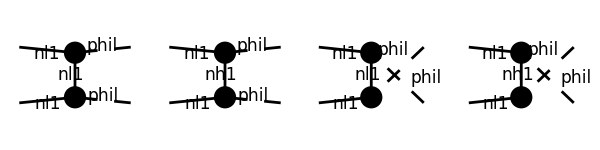

FeynArtsGraphics()(([] | [] | [] | []))

```mathematica
Paint[diagnlϕ11,ColumnsXRows->{4,1},Numbering->None,SheetHeader->False,ImageSize->{600,150}]
```

```mathematica
pmnsmat = { PMNS1x1->0.8255,PMNS1x2->0.544521,PMNS1x3->0.1485,
		PMNS2x1->-0.454214,PMNS2x2->0.484741,PMNS2x3->0.747473,
		PMNS3x1->0.334031,PMNS3x2->-0.684487,PMNS3x3->0.647481};
couplings={FCGV["EL"]->√(4 π /137),sw->√0.231,cw->√(1-0.231)};

proprep={FeynAmpDenominator[PropagatorDenominator[Momentum[p_],mN1]]:>1/(SP[p]-mN1^2),
		FeynAmpDenominator[PropagatorDenominator[-Momentum[p_],mN1]]:>1/(SP[p]-mN1^2),
		FeynAmpDenominator[PropagatorDenominator[Momentum[p_],mnl1]]:>1/(SP[p]-mnl1^2),
		FeynAmpDenominator[PropagatorDenominator[-Momentum[p_],mnl1]]:>1/(SP[p]-mnl1^2)};

kinemrep={Pair[Momentum[p1],Momentum[p2]]->1/2(s-2 mnlin^2),
		Pair[Momentum[p3],Momentum[p4]]->1/2(s-2 mnlout^2),
		Pair[Momentum[p1],Momentum[p3]]->-1/2(t-mnlin^2-mnlout^2),
		Pair[Momentum[p2],Momentum[p4]]->-1/2(t-mnlin^2-mnlout^2),
		Pair[Momentum[p1],Momentum[p4]]->-1/2(u-mnlin^2-mnlout^2),
		Pair[Momentum[p2],Momentum[p3]]->-1/2(u-mnlin^2-mnlout^2),
		Pair[Momentum[p3+p4],Momentum[p3+p4]]->s,
		Pair[Momentum[p2-p4],Momentum[p2-p4]]->t,
		Pair[Momentum[p2-p3],Momentum[p2-p3]]->u}/.{
t->-s/2+1/2(√(s-4 mnlin^2)√(s-4 mnlout^2)Cos[θ])+mnlin^2+mnlout^2,
u->-s/2-1/2(√(s-4 mnlin^2)√(s-4 mnlout^2)Cos[θ])+mnlin^2+mnlout^2}/.mnlin->0/.mnlout->mphi;
```

```mathematica
diagSIext[diag_,diagnum_]:=DiagramExtract[diag,diagnum]

RawAmpSI[diag_,diagnum_]:=
CreateFeynAmp[diagSIext[diag,diagnum]]/.{FeynAmpDenominator->FAFeynAmpDenominator,FeynAmpList->FAFeynAmpList,NonCommutative->FANonCommutative,PolarizationVector->FAPolarizationVector,DiracSpinor->Spinor}

FCampSI[diag_,diagnum_]:=DiracSimplify[FCFAConvert[RawAmpSI[diag,diagnum],List->False,DropSumOver->True,ChangeDimension->4,UndoChiralSplittings->True,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4}]]/.proprep
```

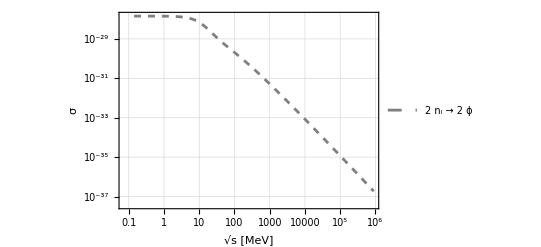

```mathematica
intamp=FCampSI[diagnlϕ11,2]+FCampSI[diagnlϕ11,4];

intamp2=DiracSimplify[FermionSpinSum[intamp ComplexConjugate[intamp]]]/.kinemrep/.{Pair[Momentum[p3],Momentum[p3]]->mphi^2,Pair[Momentum[p4],Momentum[p4]]->mphi^2}//.pmnsmat//.couplings/.{mnlin->mnl1,mnlout->mphi}//Simplify;

intamp3=intamp2/.{mnl1->6 10^-8,mN1->10,mphi->0.1,Γphi->0.01,lphiN->0.01}//Simplify;

intamp2int[sqrts_]:=NIntegrate[Sin[θ]intamp3/.s->sqrts^2,{θ,0,π}]
intamp4=ParallelTable[{√(10^ii),1/(64 π^2 s)(*(√(s-2 0.1^2)/2)/(√s/2)*)(*Phase Space*)1/4(*Spin Av.*)2π intamp2int[√(10^ii)]//.s->10^ii},{ii,Log10[0.0201],12,0.1}];
ListLogLogPlot[intamp4,Joined->True,PlotStyle->Directive[Dashed,Gray],PlotRange->All,PlotLegends->{"2 n_l → 2 ϕ"},Frame->True,FrameLabel->{"√s [MeV]","σ"},GridLines->Automatic]
```

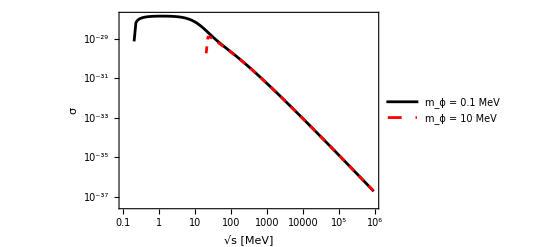

```mathematica
intamp3=(√(s-4 mphi^2)/2)/(√s/2)intamp2/.{mnl1->6 10^-8,mN1->10,mphi->0.1,Γphi->0.01,lphiN->0.01}//Simplify;
intamp3p=(√(s-4 mphi^2)/2)/(√s/2)intamp2/.{mnl1->6 10^-8,mN1->10,mphi->10,Γphi->0.01,lphiN->0.01}//Simplify;


intamp3int[sqrts_]:=NIntegrate[Sin[θ]intamp3/.s->sqrts^2,{θ,0,π}]
intamp3pint[sqrts_]:=NIntegrate[Sin[θ]intamp3p/.s->sqrts^2,{θ,0,π}]
intamp4=ParallelTable[{√(10^ii),1/(64 π^2 s)(*Phase Space*)1/4(*Spin Av.*)2π intamp3int[√(10^ii)]//.s->10^ii},{ii,Log10[0.0201],12,0.1}];
intamp4p=ParallelTable[{√(10^ii),1/(64 π^2 s)(*Phase Space*)1/4(*Spin Av.*)2π intamp3pint[√(10^ii)]//.s->10^ii},{ii,Log10[0.0201],12,0.1}];
ListLogLogPlot[{intamp4,intamp4p},Joined->True,PlotStyle->{Black,Directive[Dashed,Red]},PlotRange->All,PlotLegends->{"m_ϕ = 0.1 MeV","m_ϕ = 10 MeV"},Frame->True,FrameLabel->{"√s [MeV]","σ"},GridLines->Automatic]
```

```mathematica
ampanalytic=SpinorVBar[p2].((DiracSlash[p1-p3]-mN1)/(t-mN1^2)+(DiracSlash[p1-p4]-mN1)/(u-mN1^2)).SpinorU[p1];
ampSqanalytic=DiracSimplify[FermionSpinSum[ampanalytic ComplexConjugate[ampanalytic]]]/.kinemrep/.{Pair[Momentum[p3],Momentum[p3]]->mphi^2,Pair[Momentum[p4],Momentum[p4]]->mphi^2,Pair[Momentum[p1],Momentum[p1]]->0}//.pmnsmat//.couplings/.{mnlin->mnl1,mnlout->mphi}//Simplify;
ampSqanalyticval=ampSqanalytic/.{
t->-s/2+1/2(√(s-4 mnlin^2)√(s-4 mnlout^2)Cos[θ])+mnlin^2+mnlout^2,
u->-s/2-1/2(√(s-4 mnlin^2)√(s-4 mnlout^2)Cos[θ])+mnlin^2+mnlout^2}/.mnlin->0/.mnlout->mphi/.{mnl1->6 10^-8,mN1->10,mphi->0.1,Γphi->0.01,lphiN->0.01}//Simplify;
```

```mathematica
ampSqanalytic2=ampSqanalytic/.{
t->-s/2+1/2(√(s-4 mnlin^2)√(s-4 mnlout^2)Cos[θ])+mnlin^2+mnlout^2,
u->-s/2-1/2(√(s-4 mnlin^2)√(s-4 mnlout^2)Cos[θ])+mnlin^2+mnlout^2}/.mnlin->0/.mnlout->mphi//Simplify;
ampSqanalytic2=Integrate[Sin[θ]ampSqanalytic2,{θ,0,π}];
```

```mathematica
analyticXse=1/(64 π^2 s)(√(s-4 mphi^2)/2)/(√s/2)(*Phase Space*)1/4(*Spin Av.*)2π (lphiN mnl1/mN1)^2 lphiN^2 Simplify[ampSqanalytic2,s>4 mphi^2];
```

```mathematica
repval={mnl1->6 10^-8,mN1->10,mphi->0.1,Γphi->0.01,lphiN->0.01};
```

```mathematica
ampSqSred=(lphiN mnl1/mN1)^2 lphiN^2 ampSqanalyticval/.repval//Simplify;

(*ampSqSredint = Integrate[Sin[θ]ampSqSred,{θ,0,π}];*)

SredniXsec=ParallelTable[{√(10^ii),1/(64 π^2 s)(√(s-4 0.1^2)/2)/(√s/2)(*Phase Space*)1/4(*Spin Av.*)2π NIntegrate[Sin[θ]ampSqSred/.s->10^ii,{θ,0,π}]//.s->10^ii},{ii,Log10[0.0201],12,0.1}];
```

```mathematica
fs[s_]:=√(1-4 mphi^2/s)
gis[s_]:=(mN1^2-mphi^2)/s

σs[s_,ii_]:=1/s{((8 fs[s])/(1+s/mN1^2(gis[s])^2)),24fs[s],(16(6(gis[s])^2+4gis[s]+1+4 mN1^2/s))/(1+2gis[s])ArcTanh[fs[s]/(1+2gis[s])]}[[ii]]//.{mnl1->6 10^-8,mN1->10,mphi->0.1,Γphi->0.01,lphiN->0.01}
subσ[ll_]:=ParallelTable[{√(10^ii),σs[10^ii,ll]},{ii,Log10[0.0401],12,0.1}];
lowend=ParallelTable[{√(10^ii),((lphiN mnl1/mN1)^2 lphiN^2)/(128π)Normal[Series[asd,{x,0,1}]]fs[10^ii]/.x->10^ii/mN1^2//.{mnl1->6 10^-8,mN1->10,mphi->0.1,Γphi->0.01,lphiN->0.01}},{ii,Log10[0.0401],4,0.1}];
```

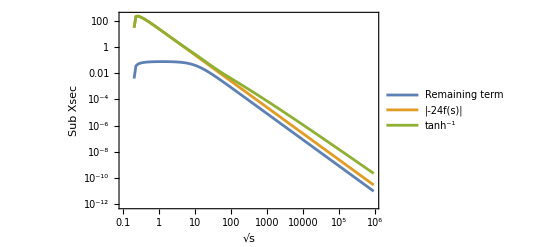

```mathematica
ListLogLogPlot[{subσ[1],subσ[2],subσ[3]},PlotLegends->{"Remaining term","|-24f(s)|","tanh^-1"},Joined->True,FrameLabel->{"√s","Sub Xsec"},Frame->True]
```

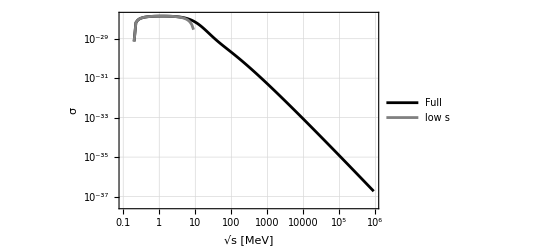

```mathematica
comparison=Table[{√(10^ii),10^-20 10^-ii},{ii,3,12,0.1}];
ListLogLogPlot[{SredniXsec,lowend},Joined->True,PlotStyle->{Black,Gray,Directive[Dashed,Red],Green},PlotRange->All,PlotLegends->{"Full","low s"},Frame->True,FrameLabel->{"√s [MeV]","σ"},GridLines->Automatic]
```

#### Amplitudes ϕ ϕ → χ χ

```mathematica
topo=CreateTopologies[0,2->2];
diagϕχ[ii_]:=InsertFields[topo,{S[2],S[2]}->{F[ii],F[ii]},InsertionLevel->{Particles},Model->modelfile,GenericModel->modelfile]
```

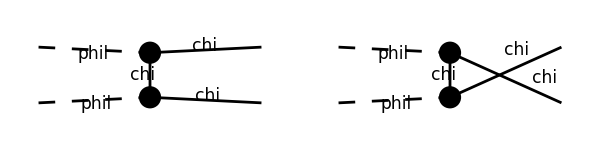

FeynArtsGraphics()(([] | [] | Null | Null))

```mathematica
Paint[diagϕχ[7],ColumnsXRows->{4,1},Numbering->None,SheetHeader->False,ImageSize->{600,150}]
```

```mathematica
proprep={FeynAmpDenominator[PropagatorDenominator[Momentum[p_],mchi]]:>1/(SP[p]-mchi^2),
		FeynAmpDenominator[PropagatorDenominator[-Momentum[p_],mchi]]:>1/(SP[p]-mchi^2)};

kinemrep={Pair[Momentum[p1],Momentum[p2]]->1/2(s-2 mnlin^2),
		Pair[Momentum[p3],Momentum[p4]]->1/2(s-2 mnlout^2),
		Pair[Momentum[p1],Momentum[p3]]->-1/2(t-mnlin^2-mnlout^2),
		Pair[Momentum[p2],Momentum[p4]]->-1/2(t-mnlin^2-mnlout^2),
		Pair[Momentum[p1],Momentum[p4]]->-1/2(u-mnlin^2-mnlout^2),
		Pair[Momentum[p2],Momentum[p3]]->-1/2(u-mnlin^2-mnlout^2),
		Pair[Momentum[p3+p4],Momentum[p3+p4]]->s,
		Pair[Momentum[p2-p4],Momentum[p2-p4]]->t,
		Pair[Momentum[p2-p3],Momentum[p2-p3]]->u}/.{
t->-s/2+1/2(√(s-4 mnlin^2)√(s-4 mnlout^2)Cos[θ])+mnlin^2+mnlout^2,
u->-s/2-1/2(√(s-4 mnlin^2)√(s-4 mnlout^2)Cos[θ])+mnlin^2+mnlout^2}/.mnlin->mphi/.mnlout->mchi;
```

```mathematica
diagSIext[diag_,diagnum_]:=DiagramExtract[diag,diagnum]

RawAmpSI[diag_,diagnum_]:=
CreateFeynAmp[diagSIext[diag,diagnum]]/.{FeynAmpDenominator->FAFeynAmpDenominator,FeynAmpList->FAFeynAmpList,NonCommutative->FANonCommutative,PolarizationVector->FAPolarizationVector,DiracSpinor->Spinor}

FCampSI[diag_,diagnum_]:=DiracSimplify[FCFAConvert[RawAmpSI[diag,diagnum],List->False,DropSumOver->True,ChangeDimension->4,UndoChiralSplittings->True,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4}]]/.proprep
```

```mathematica
intmedamp=FCampSI[diagϕχ[7],1]+FCampSI[diagϕχ[7],2];
ϕϕtoχχAmpSq=DiracSimplify[FermionSpinSum[intmedamp ComplexConjugate[intmedamp]]]/.kinemrep/.{Pair[Momentum[p2],Momentum[p2]]->mphi^2,Pair[Momentum[p3],Momentum[p3]]->mchi^2,Pair[Momentum[p4],Momentum[p4]]->mchi^2}//Simplify;
ϕϕtoχχint=Simplify[Integrate[Sin[θ]ϕϕtoχχAmpSq,{θ,0,π}],{s>0,mphi^2>0}];
```

```mathematica
ϕϕtoχχint
```

-lphichi^4 (4 mchi^2-s) ((16 (-32 mchi^4+16 mchi^2 (s-mphi^2)+6 mphi^4-4 mphi^2 s+s^2) cot^-1((2 mphi^2-s)/(√(s-4 mchi^2) √(4 mphi^2-s))))/((s-4 mchi^2)^(3/2) (2 mphi^2-s) √(4 mphi^2-s))+(8 (16 mchi^4+2 mchi^2 (s-8 mphi^2)+3 mphi^4))/((4 mchi^2-s) (mchi^2 (s-4 mphi^2)+mphi^4)))

```mathematica
((8 (16 mchi^4+2 mchi^2 (s-8 mphi^2)+3 mphi^4))/((mchi^2 (s-4 mphi^2)+mphi^4)))//FullSimplify
```

(8 (mphi^2-4 mchi^2)^2)/(mchi^2 (s-4 mphi^2)+mphi^4)+16

```mathematica
abc=1/(64 π^2 s)2π 1/4(√(s-4 mchi^2)/2)/(√s/2)ϕϕtoχχint/.{mphi->10^-4,mchi->10^-2,lphichi->0.01}//N;
```

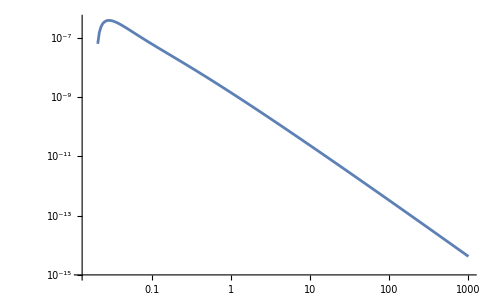

```mathematica
ListLogLogPlot[ParallelTable[{10^ii,Re[abc/.s->10^(2ii)]},{ii,-2,3,0.02}],Joined->True]
```

#### Amplitudes χ χ → χ χ

```mathematica
topo=CreateTopologies[0,2->2];
diagχSI=InsertFields[topo,{F[7],F[7]}->{F[7],F[7]},InsertionLevel->{Particles},Model->modelfile,GenericModel->modelfile];
```

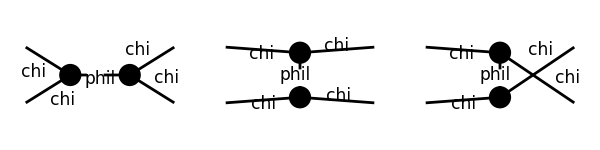

FeynArtsGraphics()(([] | [] | [] | Null))

```mathematica
Paint[diagχSI,ColumnsXRows->{4,1},Numbering->None,SheetHeader->False,ImageSize->{600,150}]
```

```mathematica
proprep={FeynAmpDenominator[PropagatorDenominator[Momentum[p_],mphi]]:>1/(SP[p]-mphi^2+ⅈ mphi Γphi),
		FeynAmpDenominator[PropagatorDenominator[-Momentum[p_],mphi]]:>1/(SP[p]-mphi^2+ⅈ mphi Γphi)};

kinemrep={Pair[Momentum[p1],Momentum[p2]]->1/2(s-2 mnlin^2),
		Pair[Momentum[p3],Momentum[p4]]->1/2(s-2 mnlout^2),
		Pair[Momentum[p1],Momentum[p3]]->-1/2(t-mnlin^2-mnlout^2),
		Pair[Momentum[p2],Momentum[p4]]->-1/2(t-mnlin^2-mnlout^2),
		Pair[Momentum[p1],Momentum[p4]]->-1/2(u-mnlin^2-mnlout^2),
		Pair[Momentum[p2],Momentum[p3]]->-1/2(u-mnlin^2-mnlout^2),
		Pair[Momentum[p3+p4],Momentum[p3+p4]]->s,
		Pair[Momentum[p2-p4],Momentum[p2-p4]]->t,
		Pair[Momentum[p2-p3],Momentum[p2-p3]]->u}(*/.{
t->-s/2+1/2(√(s-4 mnlin^2)√(s-4 mnlout^2)Cos[θ])+mnlin^2+mnlout^2,
u->-s/2-1/2(√(s-4 mnlin^2)√(s-4 mnlout^2)Cos[θ])+mnlin^2+mnlout^2}*)/.mnlin->0/.mnlout->0;
tusub={t->-s/2+1/2(√(s-4 mnlin^2)√(s-4 mnlout^2)Cos[θ])+mnlin^2+mnlout^2,
u->-s/2-1/2(√(s-4 mnlin^2)√(s-4 mnlout^2)Cos[θ])+mnlin^2+mnlout^2}/.mnlin->0/.mnlout->0;
```

```mathematica
diagSIext[diag_,diagnum_]:=DiagramExtract[diag,diagnum]

RawAmpSI[diag_,diagnum_]:=
CreateFeynAmp[diagSIext[diag,diagnum]]/.{FeynAmpDenominator->FAFeynAmpDenominator,FeynAmpList->FAFeynAmpList,NonCommutative->FANonCommutative,PolarizationVector->FAPolarizationVector,DiracSpinor->Spinor}

FCampSI[diag_,diagnum_]:=DiracSimplify[FCFAConvert[RawAmpSI[diag,diagnum],List->False,DropSumOver->True,ChangeDimension->4,UndoChiralSplittings->True,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4}]]/.proprep
```

```mathematica
FCampSI[diag_,diagnum_]:=DiracSimplify[FCFAConvert[RawAmpSI[diag,diagnum],List->False,DropSumOver->True,ChangeDimension->4,UndoChiralSplittings->True,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4}]]

χSIamp=FCampSI[diagχSI,1]+FCampSI[diagχSI,2]+FCampSI[diagχSI,3]/.{FeynAmpDenominator[PropagatorDenominator[Momentum[p_],mphi]]:>1/-mphi^2,
		FeynAmpDenominator[PropagatorDenominator[-Momentum[p_],mphi]]:>1/-mphi^2};
χSIampSq=DiracSimplify[FermionSpinSum[χSIamp ComplexConjugate[χSIamp]]]/.kinemrep/.{Pair[Momentum[p3],Momentum[p3]]->mchi^2,Pair[Momentum[p4],Momentum[p4]]->mchi^2}/.{mnlin->mchi,mnlout->mchi}/.mchi->0//ComplexExpand//Simplify;
χSIampSq
```

(2 lphichi^4 (s^2+t^2+u^2))/mphi^4

```mathematica
χSIamp=FCampSI[diagχSI,1]+FCampSI[diagχSI,2]+FCampSI[diagχSI,3];
χSIampSq=DiracSimplify[FermionSpinSum[χSIamp ComplexConjugate[χSIamp]]]/.kinemrep/.tusub/.{Pair[Momentum[p3],Momentum[p3]]->mchi^2,Pair[Momentum[p4],Momentum[p4]]->mchi^2}/.{mnlin->mchi,mnlout->mchi}/.mchi->0//ComplexExpand//Simplify;

int=Simplify[Integrate[Sin[θ]χSIampSq/.tusub,{θ,0,π}],{s>Γphi^2,s>0,mphi^2>0}];
```

```mathematica
Normal[Series[Numerator[1/(64 π^2 s)2π 1/4 int],{Γphi,0,1}]]//FullSimplify
```

lphichi^4 ((s (5 mphi^6-9 mphi^4 s+6 s^3))/(mphi^2+s)+(mphi^2 (5 mphi^6-9 mphi^4 s+4 s^3) (log(mphi^4)-log((mphi^2+s)^2)))/(2 mphi^2+s))

```mathematica
Denominator[1/(64 π^2 s)2π 1/4 int]//FullSimplify
```

16 π s^2 (Γphi^2 mphi^2+(mphi^2-s)^2)

```mathematica
Normal[Series[Numerator[1/(64 π^2 s)2π 1/4 int],{Γphi,0,1}]]//FullSimplify
```

lphichi^4 ((s (5 mphi^6-9 mphi^4 s+6 s^3))/(mphi^2+s)+(mphi^2 (5 mphi^6-9 mphi^4 s+4 s^3) (log(mphi^4)-log((mphi^2+s)^2)))/(2 mphi^2+s))

```mathematica
s (6 mphi^6-13 mphi^4 s+4 mphi^2 s^2+6 s^3)/(2 mphi^2+s)//Simplify
```

s (3 mphi^4-8 mphi^2 s+6 s^2)

```mathematica
1/(64 π^2 s)2π 1/4 Normal[Series[int,{Γphi,0,1}]]//Simplify
```

1/(16 π s^2 (mphi^2-s)^2 (mphi^2+s) (2 mphi^2+s))lphichi^4 (s (10 mphi^8-13 mphi^6 s-9 mphi^4 s^2+12 mphi^2 s^3+6 s^4)+mphi^2 (5 mphi^8-4 mphi^6 s-9 mphi^4 s^2+4 mphi^2 s^3+4 s^4) log(mphi^4)+(-5 mphi^10+4 mphi^8 s+9 mphi^6 s^2-4 mphi^4 s^3-4 mphi^2 s^4) log((mphi^2+s)^2))

```mathematica
σEFTχSI=Normal[Series[1/(64 π^2 s)2π 1/4 int,{s,0,1}]]/.Γphi->0//Simplify
```

(5 lphichi^4 s)/(96 π mphi^4)

```mathematica
vals = χSIampSq/.lphichi->0.3/.Γphi->0.001/.mphi->0.1/.mchi->0;
σχSI=1/(64 π^2 s)2π 1/4 Normal[Series[int,{Γphi,0,1}]]/.lphichi->0.3/.Γphi->0.001/.mphi->0.1/.mchi->0//Simplify;
```

```mathematica
χSItab=ParallelTable[{√(10^ii),1/(64 π^2 10^ii)(*Phase Space*)1/4(*Spin Av.*)2π (*ϕ Int*)NIntegrate[Sin[θ]vals/.s->10^ii,{θ,0,π}]},{ii,-8,3,0.01}];

σχSIapptab=ParallelTable[{√(10^ii),σχSI/.s->10^ii},{ii,-8.001,3.001,0.01}];
```

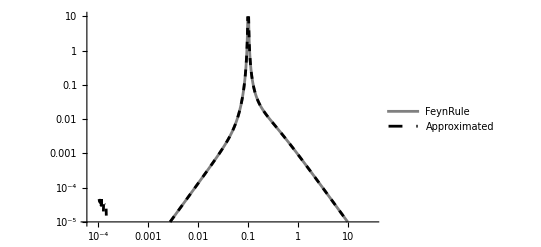

```mathematica
ListLogLogPlot[{χSItab,σχSIapptab},Joined->True,PlotStyle->{Gray,Directive[Dashed,Black]},PlotRange->{10^-5,10^1},PlotLegends->{"FeynRule","Approximated"}]
```

#### Amplitudes n_l n_l → ϕ

```mathematica
(* Decay width *)
topo=CreateTopologies[0,1->2];
decaydiag[ii_]:=InsertFields[topo,{S[2]}->{F[ii],F[ii]},InsertionLevel->{Particles},Model->modelfile,GenericModel->modelfile]
```

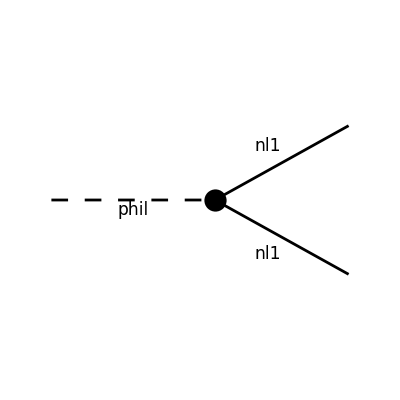

FeynArtsGraphics()(([] | Null | Null | Null))

```mathematica
Paint[decaydiag[1],ColumnsXRows->{4,1},Numbering->None,SheetHeader->False,ImageSize->{600,150}]
```

```mathematica
proprep={FeynAmpDenominator[PropagatorDenominator[Momentum[p_],mphi]]:>1/(SP[p]-mphi^2+ⅈ mphi Γphi),
		FeynAmpDenominator[PropagatorDenominator[-Momentum[p_],mphi]]:>1/(SP[p]-mphi^2+ⅈ mphi Γphi)};

kinemrep={Pair[Momentum[p1],Momentum[p2]]->1/2(s-2 mnlin^2),
		Pair[Momentum[p3],Momentum[p4]]->1/2(s-2 mnlout^2),
		Pair[Momentum[p1],Momentum[p3]]->-1/2(t-mnlin^2-mnlout^2),
		Pair[Momentum[p2],Momentum[p4]]->-1/2(t-mnlin^2-mnlout^2),
		Pair[Momentum[p1],Momentum[p4]]->-1/2(u-mnlin^2-mnlout^2),
		Pair[Momentum[p2],Momentum[p3]]->-1/2(u-mnlin^2-mnlout^2),
		Pair[Momentum[p3+p4],Momentum[p3+p4]]->s,
		Pair[Momentum[p2-p4],Momentum[p2-p4]]->t,
		Pair[Momentum[p2-p3],Momentum[p2-p3]]->u}/.{
t->-s/2+1/2(√(s-4 mnlin^2)√(s-4 mnlout^2)Cos[θ])+mnlin^2+mnlout^2,
u->-s/2-1/2(√(s-4 mnlin^2)√(s-4 mnlout^2)Cos[θ])+mnlin^2+mnlout^2}/.mnlin->mphi/.mnlout->mnl1;
```

```mathematica
diagSIext[diag_,diagnum_]:=DiagramExtract[diag,diagnum]

RawAmpSI[diag_,diagnum_]:=
CreateFeynAmp[diagSIext[diag,diagnum]]/.{FeynAmpDenominator->FAFeynAmpDenominator,FeynAmpList->FAFeynAmpList,NonCommutative->FANonCommutative,PolarizationVector->FAPolarizationVector,DiracSpinor->Spinor}

FCampSI[diag_,diagnum_]:=DiracSimplify[FCFAConvert[RawAmpSI[diag,diagnum],List->False,DropSumOver->True,ChangeDimension->4,UndoChiralSplittings->True,IncomingMomenta->{p1},OutgoingMomenta->{p2,p3}]]/.proprep
```

```mathematica
decayampSq=DiracSimplify[FermionSpinSum[FCampSI[decaydiag[1],1] ComplexConjugate[FCampSI[decaydiag[1],1]]]]/.Pair[Momentum[p2],Momentum[p3]]->2 mphi^2+mnl1^2//Simplify;
```

```mathematica
mphi^2/(2 (2π)^3 Temp^2)((4 lphiN^2 mnl1^2 mphi)/(π mN1^2))BesselK[1,mphi/Temp]
```

(lphiN^2 mnl1^2 mphi^3 1mphi/Temp)/(4 π^4 mN1^2 Temp^2)

```mathematica
mphi/(32 π^2 Temp^2)decayampSq BesselK[1,mphi/Temp]
```

(4 lphiN^2 mnl1^2 mphi^3 1mphi/Temp)/(π mN1^2 Temp^2)

```mathematica
intRate=(4π mphi)/(32 π^2 Temp^2)decayampSq BesselK[1,mphi/Temp]/.mphi->0.1/.mnl1->6 10^-7/.mN1->10/.lphiN->0.01;
```

```mathematica
mphi^3/(16π Temp^2)(mnl1^2+mnl2^2+mnl3^2)BesselK[1,mphi/Temp]
```

```mathematica
(4 lphiN^2 mnl1^2 mphi)/(π mN1^2)/.mN1->10/.mphi->0.1/.mnl1->10^-7/.lphiN->0.01
(4 lphichi^2 mphi)/π /.lphichi->0.01/.mphi->0.1
```

1.27324×10^-21

0.0000127324

## Trash

```mathematica
schan=lphichi^2/(s-mphi^2+ⅈ mphi Γphi)(SpinorVBar[p2].SpinorU[p1])(SpinorUBar[p3].SpinorV[p4]);
tchan=lphichi^2/(t-mphi^2+ⅈ mphi Γphi)(SpinorUBar[p3].SpinorU[p1])(SpinorUBar[p4].SpinorU[p2]);
uchan=(-1)lphichi^2/(u-mphi^2+ⅈ mphi Γphi)(SpinorUBar[p4].SpinorU[p1])(SpinorUBar[p3].SpinorU[p2]);
```

```mathematica
SIAmp=schan+tchan+uchan;
SIampSq=DiracSimplify[FermionSpinSum[SIAmp ComplexConjugate[SIAmp]]]/.{Pair[Momentum[p3],Momentum[p3]]->mchi^2,Pair[Momentum[p4],Momentum[p4]]->mchi^2}/.kinemrep/.tusub/.{mnlin->mchi,mnlout->mchi}/.mchi->0//ComplexExpand//Simplify;
```

```mathematica
val2=SIampSq//.{
t->-s/2+1/2(√(s-4 mnlin^2)√(s-4 mnlout^2)Cos[θ])+mnlin^2+mnlout^2,
u->-s/2-1/2(√(s-4 mnlin^2)√(s-4 mnlout^2)Cos[θ])+mnlin^2+mnlout^2}/.mnlin->0/.mnlout->0/.lphichi->0.3/.Γphi->0.001/.mphi->0.1/.mchi->0//Simplify;

val3=SIampSq//.{
t->-s/2+1/2(√(s-4 mnlin^2)√(s-4 mnlout^2)Cos[θ])+mnlin^2+mnlout^2,
u->-s/2-1/2(√(s-4 mnlin^2)√(s-4 mnlout^2)Cos[θ])+mnlin^2+mnlout^2}/.mnlin->0/.mnlout->0/.lphichi->0.3/.Γphi->0/.mphi->0.1/.mchi->0//Simplify;
```

```mathematica
χSI22tab=ParallelTable[{√(10^ii),1/(64 π^2 10^ii)(*Phase Space*)1/4(*Spin Av.*)2π (*ϕ Int*)NIntegrate[Sin[θ]val2/.s->10^ii,{θ,0,π}]},{ii,-8,3,0.01}];
χSI33tab=ParallelTable[{√(10^ii),1/(64 π^2 10^ii)(*Phase Space*)1/4(*Spin Av.*)2π (*ϕ Int*)NIntegrate[Sin[θ]val3/.s->10^ii,{θ,0,π}]},{ii,-8.001,3.001,0.01}];
```

$Aborted

```mathematica
integrand[Temp1_,Temp2_]:= 1/(4 (2π)^4)analyticXse s^2 (Temp1 BesselK[2,√s/Temp1]-Temp2 BesselK[2,√s/Temp2])
```

10.4642

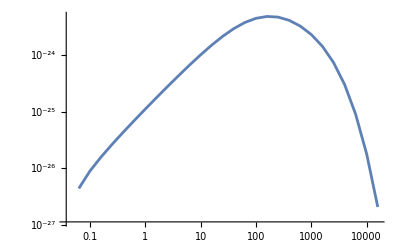

```mathematica
integrandv=integrand[10,0.001]/.{mnl1->3 10^-8,mN1->10,mphi->0.1,Γphi->0.0,lphiN->0.1};
1.5193 10^21 NIntegrate[integrandv,{s,4 0.1^2,10000}]
list =ParallelTable[{10^ii,integrandv/.s->10^ii},{ii,-3,4.3,0.2}];
ListLogLogPlot[Re[list],Joined->True]
```

10.4362

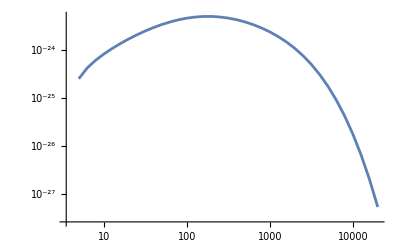

```mathematica
integrandv=integrand[10,0.001]/.{mnl1->3 10^-8,mN1->10,mphi->1,Γphi->0.01,lphiN->0.1};
1.5193 10^21 NIntegrate[integrandv,{s,4 1^2,10000}]
list =ParallelTable[{10^ii,integrandv/.s->10^ii},{ii,-3,4.3,0.1}];
ListLogLogPlot[Re[list],Joined->True]
```